155

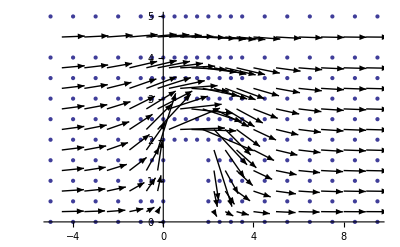

```mathematica
Clear[i,eList,α,β,γ,δ,x,y,h,j,k,gradList,R,K,A]
dir =NotebookDirectory[];
AppendTo[$Path,ToFileName[{$HomeDirectory, dir}]];
(*Elements=Import["ChnlElem.dat"];
Nodes=Import["ChnlNodes.dat"];*)
Elements = Import["C:\\Users\\Owner\\Documents\\786\\FEM\\ChnlElem.dat"];
Nodes = Import["C:\\Users\\Owner\\Documents\\786\\FEM\\ChnlNodes.dat"];
minX=Min[Nodes[[All,2]]];
maxX=Max[Nodes[[All,2]]];

lRows=4;
K=ConstantArray[0,{Length[Nodes],Length[Nodes]}];
(*188 length 0 matrix R*)
R=ConstantArray[0,{Length[Nodes]}];
eList={};
i=1;
While[i≤Length[Elements],
Subscript[v, i1]={Nodes[[Elements[[i]][[2]]]][[2]] ,Nodes[[Elements[[i]][[2]]]][[3]]};
Subscript[v, i2]={Nodes[[Elements[[i]][[3]]]][[2]],Nodes[[Elements[[i]][[3]]]][[3]]};
Subscript[v, i3]={Nodes[[Elements[[i]][[4]]]][[2]],Nodes[[Elements[[i]][[4]]]][[3]]};
Subscript[v, i4]={Nodes[[Elements[[i]][[5]]]][[2]],Nodes[[Elements[[i]][[5]]]][[3]]};
Subscript[E, i]={Subscript[v, i1],Subscript[v, i2],Subscript[v, i3],Subscript[v, i4]};

AppendTo[eList,Subscript[E, i]];
α=Subscript[v, i1][[1]];
β=Subscript[v, i1][[2]];
γ=Subscript[v, i3][[1]];
δ=Subscript[v, i3][[2]];
(*Print["α = ",α];
Print["β = ", β];
Print["γ = ", γ];
Print["δ = ",δ];*)
Subscript[ϕ, 1][x_,y_]=(γ-x)/(γ-α)*(δ-y)/(δ-β);
Subscript[ϕ, 2][x_,y_]=(x-α)/(γ-α)*(δ-y)/(δ-β);
Subscript[ϕ, 3][x_,y_]=(x-α)/(γ-α)*(y-β)/(δ-β);
Subscript[ϕ, 4][x_,y_]=(γ-x)/(γ-α)*(y-β)/(δ-β);

Subscript[gradϕ, 1][x_,y_]={D[Subscript[ϕ, 1][x,y],x],D[Subscript[ϕ, 1][x,y],y]};
Subscript[gradϕ, 2][x_,y_]={D[Subscript[ϕ, 2][x,y],x],D[Subscript[ϕ, 2][x,y],y]};
Subscript[gradϕ, 3][x_,y_]={D[Subscript[ϕ, 3][x,y],x],D[Subscript[ϕ, 3][x,y],y]};
Subscript[gradϕ, 4][x_,y_]={D[Subscript[ϕ, 4][x,y],x],D[Subscript[ϕ, 4][x,y],y]};
Subscript[gradϕlist, i]={Subscript[gradϕ, 1],Subscript[gradϕ, 2],Subscript[gradϕ, 3],Subscript[gradϕ, 4]};
gradList=ConstantArray[0,{lRows,2}];

(*get residual vector R along the trailing edge incoming flow*)
If[Nodes[[Elements[[i,5]],2]]==minX,
(*R[[Nodes[[Elements[[i,5]],1]]]]+=∫_δ^β -1*Subscript[ϕ, 4][α,y]ⅆy;*)
R[[Nodes[[Elements[[i,5]],1]]]]+=(β-δ)*Subscript[ϕ, 4][α,(β+δ)/2];
];
If[Nodes[[Elements[[i,2]],2]]==minX,
R[[Nodes[[Elements[[i,2]],1]]]]+=(β-δ)*Subscript[ϕ, 1][α,(β+δ)/2];
];

If[Nodes[[Elements[[i,3]],2]]==maxX,
R[[Nodes[[Elements[[i,3]],1]]]]+=(δ-β)*Subscript[ϕ, 2][γ,(β+δ)/2];
];
If[Nodes[[Elements[[i,4]],2]]==maxX,
(*R[[Nodes[[Elements[[i,4]],1]]]]=∫_β^δ 1*Subscript[ϕ, 3][γ,y]ⅆy;*)
R[[Nodes[[Elements[[i,4]],1]]]]+=(δ-β)*Subscript[ϕ, 3][γ,(β+δ)/2];
];


localK=ConstantArray[0,{lRows,lRows}];
j=1;
(*assemble local K matrix*)
(*Print["Now on element ",i];*)
While[j≤lRows,
	k=1;
	While[k≤lRows,
		(*Subscript[K, i][[j]][[k]]=(∫_γ)^δ((∫_α)^β Subscript[gradϕ, j][x,y].Subscript[gradϕ, k][x,y]ⅆx)ⅆy;*)
		localK[[j,k]]=∫_β^δ (∫_α^γ Subscript[gradϕ, j][x,y].Subscript[gradϕ, k][x,y]ⅆx)ⅆy;
(*Print[Subscript[gradϕ, j][α,β].Subscript[gradϕ, k][α,β]];*)
			k++;
		];
	j++;
	];

(*assemble global matrix K*)
(*Print[i];*)
(*Print["localK is ",MatrixForm[localK]];*)
h=1;
While[h≤lRows,
	w=1;
	While[w≤lRows,
		K[[Elements[[i,h+1]],Elements[[i,w+1]]]]+=localK[[h,w]];
	w++;
	];
h++;
];
i++;
]
(*Print["Residual matrix: ",MatrixForm[R]];*)
E188 = IdentityMatrix[Length[Nodes]];
K[[61]]=E188[[61]];
A=LinearSolve[K,R];

(*Show vectors and node points*)
Clear[α,β,γ,δ,i,x,y]
(*Δd=.15;*)
pList={};
cList ={};
i=1;
While[i≤Length[Elements],
	α=Subscript[E, i][[1]][[1]];
	β=Subscript[E, i][[1]][[2]];
	γ=Subscript[E, i][[3]][[1]];
	δ=Subscript[E, i][[3]][[2]];
Subscript[ϕ, 1][x_,y_]=(γ-x)/(γ-α)*(δ-y)/(δ-β);
Subscript[ϕ, 2][x_,y_]=(x-α)/(γ-α)*(δ-y)/(δ-β);
Subscript[ϕ, 3][x_,y_]=(x-α)/(γ-α)*(y-β)/(δ-β);
Subscript[ϕ, 4][x_,y_]=(γ-x)/(γ-α)*(y-β)/(δ-β);
	Subscript[a, 1]=A[[Nodes[[Elements[[i,2]],1]]]];
	Subscript[a, 2]=A[[Nodes[[Elements[[i,3]],1]]]];
	Subscript[a, 3]=A[[Nodes[[Elements[[i,4]],1]]]];
	Subscript[a, 4]=A[[Nodes[[Elements[[i,5]],1]]]];delp[n_,m_]=Subscript[a, 1]*Subscript[ϕ, 1][n,m]+Subscript[a, 2]*Subscript[ϕ, 2][n,m]+Subscript[a, 3]*Subscript[ϕ, 3][n,m]+Subscript[a, 4]*Subscript[ϕ, 4][n,m];
gdelp[n_,m_]={D[delp[n,m],n],D[delp[n,m],m]};
cList=AppendTo[cList,{(α+γ)/2+(gdelp[(α+γ)/2,(β+δ)/2][[1]]),(β+δ)/2+(gdelp[(α+γ)/2,(β+δ)/2][[2]])}];
	pList=AppendTo[pList,{(α+γ)/2,(β+δ)/2}];
(*Print[(α+γ)/2+delp[(α+γ)/2,(β+δ)/2][[1]]];*)

i++;
];
V={};
j=1;
While[j≤Length[Elements],
V=AppendTo[V,Graphics[Arrow[{pList[[j]],cList[[j]]}]]];
j++
];
Length[V]
nPlot={};
s=1;
While[s≤Length[Nodes],
nplot=AppendTo[nPlot,{Nodes[[s,2]],Nodes[[s,3]]}];
s++
];
Show[ListPlot[nPlot],V]
```